# Test data for Fit simple s-Band

This practical the same like the example discussed to get familiar with the GTPack commands for connection to SimPack. Here it is used to generate test data for the fit.

## Init

```mathematica
Needs["GroupTheory`"]
```

```mathematica
dir=NotebookDirectory[];
```

## Hamiltonian and parameters

```mathematica
ham00={{"(ss0)"+4 (Cos[π η] Cos[π ξ]+Cos[π ζ] (Cos[π η]+Cos[π ξ])) Subscript["(ssσ)", 1]+2 (Cos[2 π ζ]+Cos[2 π η]+Cos[ 2π ξ]) Subscript["(ssσ)", 2] +8 (Cos[ π ζ]Cos[ π η]Cos[ π ξ]) Subscript["(ssσ)", 3] }};
```

```mathematica
pset={{"(ss0)",0.0},{Subscript["(ssσ)", 1],1.0},{Subscript["(ssσ)", 2],0.0},{Subscript["(ssσ)", 3],0.0}};
```

If necessary export the Hamiltonian

```mathematica
GTTbToFortran[ham00,pset,3,"htbs.f90",GOVerbose->False]
```

htbs.f90

## fcc

### Definition of k-points

```mathematica
kp=GTBZPath["fcc"];kpsym=kp[[1]];
```

```mathematica
kpl=GTBZLines[kp,{7,7,7,7,7,7}];kpline=Transpose[kpl[[1]]][[3]];
```

```mathematica
kpmesh=GTBZPointMesh[2,1,"fcc"]//N;
```

89 k-points calculated

### noise on parameters (-0.25, +0.25)

```mathematica
rd=RandomReal[{-.25,.25},4]
```

{-0.239965,-0.0678652,0.0792168,0.238158}

```mathematica
{pn,parms}=Transpose[pset];dparmr={pn,parms+rd}//Transpose
```

{{(ss0),-0.239965},{(ssσ)_1,0.932135},{(ssσ)_2,0.0792168},{(ssσ)_3,0.238158}}

```mathematica
dparm1=GTTbParmExport[dparmr,"fcc_s.parm","spd Papa (-0.05,0.05)",ham00]
```

1 | 2 | 3 | 4
(ss0) | (ssσ)_1 | (ssσ)_2 | (ssσ)_3
-0.239965 | 0.932135 | 0.0792168 | 0.238158

{{(ss0),-0.239965},{(ssσ)_1,0.932135},{(ssσ)_2,0.0792168},{(ssσ)_3,0.238158}}

```mathematica
dpp={{"(ss0)",0.0536},{Subscript["(ssσ)", 1],1.1315},{Subscript["(ssσ)", 2],0.1943},{Subscript["(ssσ)", 3],0.1565}}
```

{{(ss0),0.0536},{(ssσ)_1,1.1315},{(ssσ)_2,0.1943},{(ssσ)_3,0.1565}}

```mathematica
SetDirectory[dir]
```

/Users/tpqhe/SVN_SimPack_F/applications/sb/math

```mathematica
GTWriteToFile[dparm1,"fcc_t.parm"]
```

### Band structure data

#### Symmetry points

```mathematica
hdp=ham00/. GTTbParmToRule[pset];
```

```mathematica
bands0=GTBands[hdp,kpsym,1,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues
{0,0,0} |  12.0000
{0,0,1} | -4.0000
{0,1/2,1} | -4.0000
{1/2,1/2,1/2} |  0.0000
{0,0,0} |  12.0000
{3/4,3/4,0} | -3.6570
{1,1,0} | -4.0000

```mathematica
GTTbFitExport["energ.sy",bands0]
```

number of k-points = 7

number of bands    = 1

energ.sy

### Symmetry lines

```mathematica
bands1=GTBands[hdp,kpline,1,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues
{0,0,0} |  12.0000
{0,0,1/6} |  10.9300
{0,0,1/3} |  8.0000
{0,0,1/2} |  4.0000
{0,0,2/3} |  0.0000
{0,0,5/6} | -2.9280
{0,0,1} | -4.0000
{0,1/12,1} | -4.0000
{0,1/6,1} | -4.0000
{0,1/4,1} | -4.0000
{0,1/3,1} | -4.0000
{0,5/12,1} | -4.0000
{0,1/2,1} | -4.0000
{1/12,1/2,11/12} | -3.7320
{1/6,1/2,5/6} | -3.0000
{1/4,1/2,3/4} | -2.0000
{1/3,1/2,2/3} | -1.0000
{5/12,1/2,7/12} | -0.2679
{1/2,1/2,1/2} |  0.0000
{5/12,5/12,5/12} |  0.8038
{1/3,1/3,1/3} |  3.0000
{1/4,1/4,1/4} |  6.0000
{1/6,1/6,1/6} |  9.0000
{1/12,1/12,1/12} |  11.2000
{0,0,0} |  12.0000
{1/8,1/8,0} |  10.8100
{1/4,1/4,0} |  7.6570
{3/8,3/8,0} |  3.6470
{1/2,1/2,0} |  0.0000
{5/8,5/8,0} | -2.4760
{3/4,3/4,0} | -3.6570
{19/24,19/24,0} | -3.8290
{5/6,5/6,0} | -3.9280
{7/8,7/8,0} | -3.9770
{11/12,11/12,0} | -3.9950
{23/24,23/24,0} | -4.0000
{1,1,0} | -4.0000

```mathematica
GTTbFitExport["energ.li",bands1]
```

number of k-points = 37

number of bands    = 1

energ.li

### Irreducible part of BZ

```mathematica
bands2=GTBands[hdp,kpmesh,1,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues
{0.,0.,0.} |  12.0000
{0.,0.125,0.} |  11.3900
{0.,0.25,0.} |  9.6570
{0.,0.375,0.} |  7.0610
{0.,0.5,0.} |  4.0000
{0.,0.625,0.} |  0.9385
{0.,0.75,0.} | -1.6570
{0.,0.875,0.} | -3.3910
{0.,1.,0.} | -4.0000
{0.125,0.125,0.} |  10.8100
{0.125,0.25,0.} |  9.1370
{0.125,0.375,0.} |  6.6400
{0.125,0.5,0.} |  3.6960
{0.125,0.625,0.} |  0.7506
{0.125,0.75,0.} | -1.7460
{0.125,0.875,0.} | -3.4140
{0.125,1.,0.} | -4.0000
{0.25,0.25,0.} |  7.6570
{0.25,0.375,0.} |  5.4420
{0.25,0.5,0.} |  2.8280
{0.25,0.625,0.} |  0.2153
{0.25,0.75,0.} | -2.0000
{0.25,0.875,0.} | -3.4800
{0.25,1.,0.} | -4.0000
{0.375,0.375,0.} |  3.6470
{0.375,0.5,0.} |  1.5310
{0.375,0.625,0.} | -0.5858
{0.375,0.75,0.} | -2.3800
{0.375,0.875,0.} | -3.5790
{0.375,1.,0.} | -4.0000
{0.5,0.5,0.} |  0.0000
{0.5,0.625,0.} | -1.5310
{0.5,0.75,0.} | -2.8280
{0.5,0.875,0.} | -3.6960
{0.5,1.,0.} | -4.0000
{0.625,0.625,0.} | -2.4760
{0.625,0.75,0.} | -3.2770
{0.625,0.875,0.} | -3.8120
{0.75,0.75,0.} | -3.6570
{0.125,0.125,0.125} |  10.2400
{0.125,0.25,0.125} |  8.6400
{0.125,0.375,0.125} |  6.2430
{0.125,0.5,0.125} |  3.4140
{0.125,0.625,0.125} |  0.5858
{0.125,0.75,0.125} | -1.8120
{0.125,0.875,0.125} | -3.4140
{0.125,1.,0.125} | -3.9770
{0.25,0.25,0.125} |  7.2260
{0.25,0.375,0.125} |  5.1100
{0.25,0.5,0.125} |  2.6130
{0.25,0.625,0.125} |  0.1165
{0.25,0.75,0.125} | -2.0000
{0.25,0.875,0.125} | -3.4140
{0.25,1.,0.125} | -3.9110
{0.375,0.375,0.125} |  3.4140
{0.375,0.5,0.125} |  1.4140
{0.375,0.625,0.125} | -0.5858
{0.375,0.75,0.125} | -2.2810
{0.375,0.875,0.125} | -3.4140
{0.375,1.,0.125} | -3.8120
{0.5,0.5,0.125} |  0.0000
{0.5,0.625,0.125} | -1.4140
{0.5,0.75,0.125} | -2.6130
{0.5,0.875,0.125} | -3.4140
{0.625,0.625,0.125} | -2.2430
{0.625,0.75,0.125} | -2.9450
{0.25,0.25,0.25} |  6.0000
{0.25,0.375,0.25} |  4.1650
{0.25,0.5,0.25} |  2.0000
{0.25,0.625,0.25} | -0.1648
{0.25,0.75,0.25} | -2.0000
{0.25,0.875,0.25} | -3.2260
{0.25,1.,0.25} | -3.6570
{0.375,0.375,0.25} |  2.7510
{0.375,0.5,0.25} |  1.0820
{0.375,0.625,0.25} | -0.5858
{0.375,0.75,0.25} | -2.0000
{0.375,0.875,0.25} | -2.9450
{0.5,0.5,0.25} |  0.0000
{0.5,0.625,0.25} | -1.0820
{0.5,0.75,0.25} | -2.0000
{0.625,0.625,0.25} | -1.5790
{0.375,0.375,0.375} |  1.7570
{0.375,0.5,0.375} |  0.5858
{0.375,0.625,0.375} | -0.5858
{0.375,0.75,0.375} | -1.5790
{0.5,0.5,0.375} |  0.0000
{0.5,0.625,0.375} | -0.5858
{0.5,0.5,0.5} |  0.0000

```mathematica
GTTbFitExport["energ.me",bands2]
```

number of k-points = 89

number of bands    = 1

energ.me

## Band structure

Maximum Abscissa = 4.48735

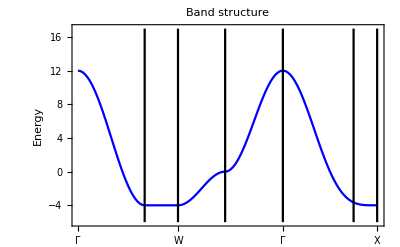

```mathematica
phfcc1=ham00 /.GTTbParmToRule[pset];kp=GTBZPath["fcc"];
mfcc=GTBandStructure[phfcc1,kp,30,1,Joined->True,PlotRange->{{0,4.5},{-6.,17.}}]
```

Maximum Abscissa = 4.48735

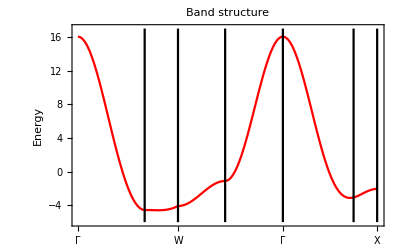

```mathematica
phfccr=ham00 /.GTTbParmToRule[dpp];kp=GTBZPath["fcc"];
mfccr=GTBandStructure[phfccr,kp,30,1,Joined->True,PlotRange->{{0,4.5},{-6.,17.}},PlotStyle->Red]
```

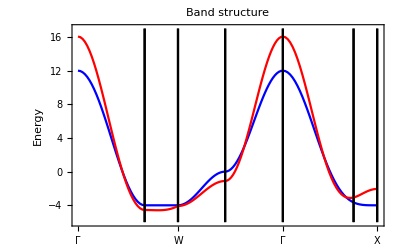

```mathematica
Show[mfcc,mfccr]
```